## 3.029 Spring 2022 Assignment 03 Due March 18nd at 1pm

## Random Walks & Polymer Dynamics

## General Instructions Reminder

Notebooks should be submitted to canvas

You can choose to submit either a Wolfram Notebook (.nb), or  a Jupyter Notebook (.ipynb)

Please name your notebook using the following notation:
3029__Assignment-03__LASTNAME_FIRSTNAME.nb

Before submitting your notebook:

Make sure all your code runs from a fresh kennel 
Wolfram Notebook: Evaluation → Quit Kernel, Evaluation → Evaluate Notebook
Jupyter Notebook: Kernel → Restart & Run All

Delete all your output
Wolfram Notebook: Cell → Delete All Output
Jupyter Notebook: Cell → All Output → Clear

Tips to maximize your score:

Comment your code well using text cells/Markdown (not in-line comments)

Don’t include extraneous code and narrative that does not contribute to the answer

But feel free to keep a ‘scratch’ notebook as you develop your solutions

Make your graphics are aesthetically pleasing and easy to read

Notably: label your axes and use legible font sizes

## Vacancy Diffusion on a Honeycomb Lattice (25 points)

### Single Vacancy Diffusion (20 points)

Consider a honeycomb lattice (graphene) with a single vacancy

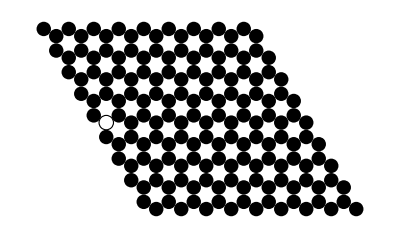

```mathematica
hexagonalLatticeVectors={{1,0},{-1/2,Sqrt[3]/2}};
honeyCombMotif={{0,0},{1/3,-1/3}};
honeycombLatticeSites=Join@@Outer[Plus,Tuples[Range[-4,4],2],honeyCombMotif,1].hexagonalLatticeVectors;
baseGraphic=Graphics[{Disk[#,1/(2 √3)]&/@honeycombLatticeSites}];

initialVacancyPosition = RandomChoice[honeycombLatticeSites];
Show[baseGraphic,Graphics[{EdgeForm[Black],FaceForm[White],Disk[initialVacancyPosition,1/(2 √3)]}]]
```

Animate a random walk on the lattice, assuming at each ‘time-step’ the vacancy can either:

Stay in place

Move to one of its three nearest-neighbors

Your solution should look something like this (you are of-course allowed/encouraged to make it look prettier!):

Note the solution below implements ‘periodic’ boundary conditions on this 9x9 honeycomb supercell

I.e. a vacancy in the bottom right position is allowed to jump to the bottom-left position (e.g. frames 334 to 335)

### Multi-Vacancy Diffusion (5 points)

Repeat the same for more than one vacancy

Note: two vacancies can’t occupy the same position!

## Temperature-Gradient Diffusion (25 points)

Consider a unit-square domain with 500 random particles and periodic boundaries in y-direction

I.e. something like this

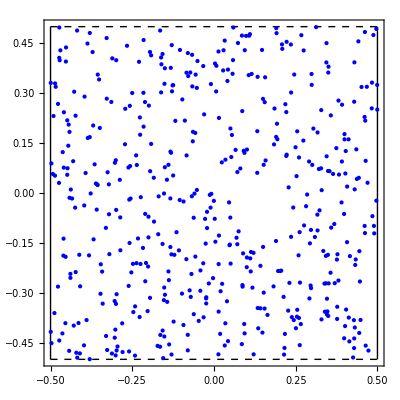

```mathematica
With[{randomPoints=RandomReal[{-1/2,1/2},{500,2}]},
Graphics[{
{Line[{{-1/2,-1/2},{-1/2,1/2}}],Line[{{1/2,-1/2},{1/2,1/2}}]},
{Dashed,Line[{{-1/2,1/2},{1/2,1/2}}],Line[{{-1/2,-1/2},{1/2,-1/2}}]},
{Blue,PointSize[Medium],Point[randomPoints]}
},Frame->True,Axes->True,PlotRangePadding->1/8]
]
```

Let the particles undergo a random-walk motion

with a step-size which depends on their distance from the left wall

Specifically, let the particles take a step-size of 0.1 at the left wall, and 0.01 at the right wall (and linearly interpolate in-between)

enforce periodic-boundary conditions in the y-direction

enforce ‘sensible’ hard-wall boundary conditions in the x-direction. Here are some options:

Specular boundary conditions (i.e. bouncing at the same angle of incidence as they hit the wall)

Diffuse boundary conditions (i.e. bouncing at a random angle back into the domain)

This simple model is related to a phenomenon called thermophoresis.

Comment on your results in the context of the Wikipedia article above!

## End-to-end distances (15 points)

### Self-avoiding random walk (10 points)

In Lecture 09, we studied the end-to-end distance of self-intersecting polymers, and found it to scale with N^(1/2)

In Lecture 10, we developed a model for a self-avoiding polymer chain

Compute the end-to-end distance scaling relation for a self-avoiding random walk in both two and three dimensions

Hint: You will need to use a similar Monte-Carlo technique like in L09 to gather enough data for statistical significance

### Random walk on a sphere (5 points)

Perform a (self-intersecting) random walk on the surface of a sphere

Note: Make sure to choose a small-enough step-size

Compute the end-to-end distance scaling relation using two different distance metrics

Euclidean distance

Great circle distance

i.e. shortest distance b/w the two points along the surface of the sphere

```mathematica
greatCircleDistance[{x1_,y1_,z1_},{x2_,y2_,z2_},radius_:1]=2 radius ArcSin[EuclideanDistance[{x1,y1,z1},{x2,y2,z2}]/(2 radius)];
```

```mathematica
Echo[RandomPoint[Sphere[],2]];
greatCircleDistance@@%
EuclideanDistance@@%%
```

{{-0.164297,-0.944164,-0.28559},{0.384584,-0.542559,-0.74681}}

0.846832

0.821755

## Step-Growth Polymerization (35 points)

### Reading & Understanding Code (10 points)

We will use the initialization functions below to run the step-growth simulation needed for the next question

These are (almost) identical to the functions we walked through together in lecture

Read the functions below and do the following:

Comment and explain what the code does. In particular, comment on the functions:

displacements

moveSingleChain

checkForCollisions

moveAllChains

Identify any particularly confusing ‘shortcuts’ the code uses like `@@` etc

#### Visualization

```mathematica
polymerLoopQ[particles_]:=Norm[particles[[1]]-particles[[-1]]]//Chop//PossibleZeroQ
```

```mathematica
chainGraphic[positions_]:= {
{Circle[#,1/2]&/@positions[[2;;-2]]},
{Disk[#,1/2]&/@positions[[{1,-1}]]}
}

chainGraphic[positions_?polymerLoopQ]:={Circle[#,1/2]&/@positions}
```

```mathematica
nestListWithMonitor[f_,init_,n_]:=Module[{it=0},
PrintTemporary[ProgressIndicator[Dynamic[it/n]]];
NestList[(it++;f[#])&,init,n]]
```

#### Correlated Polymer Microstructures

```mathematica
collisionQ[nf_NearestFunction,bondLength_:1][candidatePt_]:=First[nf[candidatePt]]<bondLength

angularRange[correlation_]:={-1,1}(1-correlation)2π/3

addCorrelatedParticleToChain[correlation_][chainSoFar_]:=Block[{
nf=Nearest[chainSoFar->"Distance"],
angleRange=angularRange[correlation],
lastAngle=ArcTan@@(chainSoFar[[-1]]-chainSoFar[[-2]]),
newAngle,candidate,collision
},

newAngle=RandomReal[angleRange]+lastAngle;
candidate=Last[chainSoFar]+AngleVector[newAngle];

collision=collisionQ[nf][candidate];
If[collision,chainSoFar,Append[chainSoFar,candidate]]

]

Clear[collisionFreeCorrelatedPolymerChain2D]
collisionFreeCorrelatedPolymerChain2D[numberUnits_,correlation_,origin_:{0,0},maxAttempts_:100]:=With[{start=Join[{origin},{AngleVector[origin,RandomReal[angularRange[correlation]]]}]},
NestWhile[addCorrelatedParticleToChain[correlation],start,Length[#]<numberUnits&,1,maxAttempts]
]

randomDimer[origin_]:=Join[{origin},{AngleVector[origin,RandomReal[2π]]}]

hexagonalDimerConfiguration[size_,linearSpacingFactor_:1]:=Block[{
hexagonalLatticeVectors={{1,0},{1/2,Sqrt[3]/2}},
latticeCoords=Tuples[linearSpacingFactor Range[-size,size,3],2],sites,cleanSize=size-3},
sites=Select[latticeCoords.hexagonalLatticeVectors,cleanSize/2>#[[1]]>-cleanSize/2&&cleanSize/2>#[[2]]>-cleanSize/2&];
randomDimer/@sites
]

randomPackingDimerConfiguration[size_,linearSpacingFactor_:1]:=Block[{
proc=HardcorePointProcess[1,3 linearSpacingFactor,2],sites,cleanSize=size-3},
sites=RandomPointConfiguration[proc,Rectangle[{-cleanSize/2,-cleanSize/2},{cleanSize/2,cleanSize/2}]]["Points"];
randomDimer/@sites
]
```

#### Single Chain Reptation

```mathematica
precompute[positions_,perturbedIndex_,s_,ν_, θ_]:= Block[
{
dp = Differences[positions],
betaList,
diffs,
reducedAngles
},
betaList =ArcTan@@@ Join[-dp[[1;;perturbedIndex-1]],dp[[perturbedIndex;;-1]]] ;
reducedAngles=θ +2 ArcCot[ⅇ^(-s+s ν)Cot[(betaList-θ)/2]];
reducedAngles=Insert[reducedAngles,θ,perturbedIndex];
Transpose@{Cos[reducedAngles],Sin[reducedAngles]}]

displacementsBase[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{newPositions,betaList,Δ  },
Δ=precompute[positionList,perturbedIndex,s,ν,θ];

newPositions[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];

newPositions[index_] := newPositions[index]=
Module[{nextIndex=index-Sign[index-perturbedIndex]},
newPositions[nextIndex] + Δ[[index]]
];

newPositions/@Range[Length[Δ]]
]
```

```mathematica
displacements[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
displacementsBase[perturbedIndex,positionList,s,ν,θ]

displacements[perturbedIndex_,positionList_?polymerLoopQ,s_,ν_,θ_]:=Block[{firstStep,angle,disp,squaredNorm,minimumS,newPositions},

firstStep=displacementsBase[perturbedIndex,positionList,s,ν,θ];
angle=ArcTan@@(firstStep[[1]]-firstStep[[-1]]);

newPositions=displacementsBase[Length[positionList],firstStep,ds,ν,angle];
disp=Subtract@@newPositions[[{1,-1}]];
squaredNorm=disp.disp;

enforceClosedLoopEnd[newPositions/.First[Quiet[FindRoot[squaredNorm,{ds,s,0.,1.},AccuracyGoal->4,PrecisionGoal->4]]]]
]

enforceClosedLoopEnd[positionList_]:=ReplacePart[positionList,Length[positionList]->positionList[[1]]]
```

```mathematica
collisionFreeQ[positions_]:=With[{nf=Nearest[positions]},Total[Length[nf[#,{All,1.-10^-6}]]&/@positions]<=Length[positions]]

collisionFreeLoopQ[positions_?polymerLoopQ]:=collisionFreeQ[Most[positions]]

endPointsCollisionQ[positions_]:=With[{dr=positions[[1]]-positions[[-1]]},dr.dr<1]

mergeEndPointsSingle[positions_]:=Append[positions,First[positions]]

moveSingleChain[positions_,ds_,stickiness_,size_,forbidLoops_:False]:= 
Block[{newPositions,cleanSize=size-1},

newPositions= displacements[RandomInteger[{1,Length[positions]}],positions,ds,stickiness,RandomReal[2π]];

If[Max[Abs[MinMax[newPositions]]]>cleanSize/2,Return[positions]];

If[forbidLoops,
If[collisionFreeQ[newPositions],newPositions,positions],

If[polymerLoopQ[newPositions],If[collisionFreeLoopQ[newPositions],Return[newPositions],Return[positions]]];
If[collisionFreeQ[newPositions],Return[newPositions]];

If[endPointsCollisionQ[newPositions],
mergeEndPointsSingle[newPositions]
,positions]
]

]
```

#### Multiple Chain Reptation

```mathematica
axesAlignedBoundingBoxes[positions_]:={{-1/2,1/2},{-1/2,1/2}}+MinMax/@Transpose[positions]

horizontalAxesAlignedIntersection[{{xMinA_,xMaxA_},{yMinA_,yMaxA_}},{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}]:=(xMaxA>xMinB&&xMinA<xMaxB)
verticalAxesAlignedIntersection[{{xMinA_,xMaxA_},{yMinA_,yMaxA_}},{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}]:=(yMaxA>yMinB&&yMinA<yMaxB)

connectivityMatrixIndexHorizontal[bbs_,{i_,j_}]:=horizontalAxesAlignedIntersection[bbs[[i]],bbs[[j]]]
connectivityMatrixIndexVertical[bbs_,{i_,j_}]:=verticalAxesAlignedIntersection[bbs[[i]],bbs[[j]]]//Boole

connectivityMatrix[bbs_]:=Block[{s=Subsets[Range[Length[bbs]],{2}],l=Length[bbs],pruneHorizontally},
pruneHorizontally=Select[s,connectivityMatrixIndexHorizontal[bbs,#]&];
SparseArray[pruneHorizontally->(connectivityMatrixIndexVertical[bbs,#]&/@pruneHorizontally),{l,l}]
]

returnPointsInOverlap[{positionsA_,{{xMinA_,xMaxA_},{yMinA_,yMaxA_}}},{positionsB_,{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}}]:=With[
{
xMin=Max[xMinA,xMinB]-1/2,yMin=Max[yMinA,yMinB]-1/2,
xMax=Min[xMaxA,xMaxB]+1/2,yMax=Min[yMaxA,yMaxB]+1/2
},
Table[Select[Thread[{pos,Range[Length[pos]]}],xMax>#[[1,1]]>xMin&&yMax>#[[1,2]]>yMin&],{pos,{positionsA,positionsB}}]
]

returnAllCollisions[posA_,posB_]:=Block[{nf,sorted,
posShortcoords,posShortIndices,
posLongcoords,posLongIndices,
cols},

sorted=SortBy[{posA,posB},Length];
posShortcoords=sorted[[1,All,1]];posShortIndices=sorted[[1,All,2]];
posLongcoords=sorted[[2,All,1]];posLongIndices=sorted[[2,All,2]];

nf=Nearest[posLongcoords->{"Index","Distance"}];
cols=Select[Prepend[First[nf[posShortcoords[[#]]]],#]&/@Range[Length[posShortcoords]],#[[3]]<1&];

{posLongIndices[[#2]],posShortIndices[[#1]],#3}&@@@cols

]

pairwiseChainCollisions[{listOfPositions_,bbs_},{i_,j_}]:=Block[{
posA=listOfPositions[[i]],bbA=bbs[[i]],
posB=listOfPositions[[j]],bbB=bbs[[j]]
},

{posA,posB}=returnPointsInOverlap[{posA,bbA},{posB,bbB}];
If[Length[posA]==0||Length[posB]==0,{},returnAllCollisions[posA,posB]]
]
```

```mathematica
compareEndPoints[listOfPositions_,{i_,j_}]:=
Block[{
endsI=listOfPositions[[i,{1,-1}]],
endsJ=listOfPositions[[j,{1,-1}]],
vecs},

vecs=Tuples[{endsI,endsJ}];
Thread[SquaredEuclideanDistance@@@vecs<1]
]

mergeEndPoints[listOfPositions_,{i_,j_},pairwiseEndPointChecks_]:=With[{posI=listOfPositions[[i]],posJ=listOfPositions[[j]]},
Switch[pairwiseEndPointChecks,
{True,_,_,_},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{Reverse[posI],posJ}]],
{False,True,_,_},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{posJ,posI}]],
{False,False,True,_},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{posI,posJ}]],
{False,False,False,True},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{posI,Reverse[posJ]}]],
_,listOfPositions
]
]

collisionFreeFurtherQ[positions_]:=With[{nf=Nearest[positions->All],l=Length[positions]},
Length[Join@@Table[Select[nf[positions[[i]],{All,1}],Abs[#Index-i]>1&],{i,l}]]==0]

checkProposedMerger[{i_,j_},{posI_,posJ_}]:=
With[{proposal=Join[posI,posJ]},
If[collisionFreeFurtherQ[proposal],{{i},{j}}->proposal,Echo["Intersecting Merger"];{}]
]
```

```mathematica
checkForCollisions[{listOfPositions_,oldListOfPositions_},forbidLoops_:False]:=Catch[
Block[{
listOfPos=listOfPositions,
bbs=axesAlignedBoundingBoxes/@listOfPositions,
mij,nonzero,collisions,collisionIndices,endpointChecks,lengths},

mij=connectivityMatrix[bbs];
If[mij["ExplicitLength"]==0,Echo["No Bounding Box Collisions"];Return[listOfPos]];

nonzero=mij["NonzeroPositions"];
collisions=pairwiseChainCollisions[{listOfPos,bbs},#]&/@nonzero;
If[Length[Join@@collisions]==0,Echo["No Collisions"];Return[listOfPos]];

lengths=Sort[Length/@Extract[listOfPos,List/@#]]&/@nonzero;

If[Not[forbidLoops],
Do[
If[
Length[collisions[[a]]]>0&&
Or@@polymerLoopQ/@Extract[listOfPos,List/@nonzero[[a]]],
Echo["Collision with loop"];Throw[oldListOfPositions]],{a,Length[collisions]}]
];

Do[
If[
Length[collisions[[a]]]>0&&
(1<collisions[[a,j,1]]<lengths[[a,1]]||
1<collisions[[a,j,2]]<lengths[[a,2]]),
Echo["No-terminating collisions"];Throw[oldListOfPositions]],{a,Length[collisions]},{j,Length[collisions[[a]]]}];

collisionIndices= Extract[nonzero,Position[collisions,Except[{}],1,Heads->False]];
endpointChecks=compareEndPoints[listOfPos,#]&/@collisionIndices;
If[Nor@@Flatten[endpointChecks],Echo["No Mergers"];Return[oldListOfPositions]];

Do[
listOfPos=mergeEndPoints[listOfPos,collisionIndices[[a]],endpointChecks[[a]]],
{a,Length[collisionIndices]}
];

DeleteDuplicates[listOfPos]
]
]

moveAllChains[listOfPositions_,ds_,stickiness_,size_,forbidLoops_:False]:= Block[{listOfPos=listOfPositions},
listOfPos=moveSingleChain[#,ds,stickiness,size,forbidLoops]&/@listOfPos;
checkForCollisions[{listOfPos,listOfPositions},forbidLoops]
]
```

### Analyzing Step-Growth Polymerization Datasets (25 points)

The following runs a Dynamic simulation of step-growth without allowing for self-loops

```mathematica
boxSize=55;
listOfPositions=randomPackingDimerConfiguration[boxSize,2];

Dynamic[Graphics[{
chainGraphic/@listOfPositions,
{EdgeForm[Directive[Dashed,Black]],FaceForm[None],Rectangle[{-boxSize,-boxSize}/2,{boxSize,boxSize}/2]}
},PlotRange->All,ImageSize->350,PlotRangePadding->1]]
```

```mathematica
QuietEcho[
Do[
listOfPositions=moveAllChains[listOfPositions,0.1,0.1,boxSize,True(*Forbids Self Loops*)],
{10000}]
]
```

$Aborted

Note: `QuietEcho` silences a lot of the Debugging `Echo` statements the code uses

Try taking it out to see what it does

Similarly, this runs a Dynamic simulation while allowing for self-loops

```mathematica
boxSize=55;
listOfPositions=randomPackingDimerConfiguration[boxSize,2];

Dynamic[Graphics[{
chainGraphic/@listOfPositions,
{EdgeForm[Directive[Dashed,Black]],FaceForm[None],Rectangle[{-boxSize,-boxSize}/2,{boxSize,boxSize}/2]}
},PlotRange->All,ImageSize->350,PlotRangePadding->1]]
```

```mathematica
QuietEcho[
Do[
listOfPositions=moveAllChains[listOfPositions,0.1,0.1,boxSize,False(*Allows Self Loops*)],
{10000}]
]
```

$Aborted

Note, you probably only want to have one dynamic simulation on the screen at each time

Otherwise the Front-end might crash

Perhaps more useful - the following performs a simulation for a fixed number of steps and returns all the results

```mathematica
positions=QuietEcho[nestListWithMonitor[moveAllChains[#,0.1,0.1,boxSize,False]&,listOfPositions,1000]];
```

```mathematica
Length[positions]
```

1001

Additionally, over the next couple of days, I will upload simulation data that I have precomputed on the cloud, if that’s easier

and update the pset notebook on canvas with a link to download them

Using these functions, analyze step-growth simulations and answer the following:

Plot the average molecular weight (polymer chain length) vs % conversion (a proxy for time)

Plot the distribution of polymer chain lengths as the simulation progresses

Does the model capture all salient features of step-growth polymerization?

What is it missing if not?

How do the results change when you allow / forbid self-loops?

How do you expect the simulation results to change in 3D?

Briefly outline (using pseudocode) how you would change the simulation to have multiple reacting species

E.g A-A dimers which can react with B-B dimers to form ABBA tetramers etc